```mathematica
Clear[ProgressMap]
ProgressMap[f_, l_List]:=Module[{stdout=PrintTemporary[""], len=Length[l], begin=TimeObject[], cur, avg,eta},
Table[NotebookDelete[stdout]; cur=TimeObject[];avg=(cur-begin)/i;eta=begin+len*avg;stdout=PrintTemporary["Step "<>ToString[i]<>"/"<>ToString[len]<>" ("<>ToString[N[100*i/len]]<>"% complete, Avg Time "<>ToString[QuantityMagnitude[avg,"Seconds"]]<>" seconds per elem, ETA "<>DateString[eta, "DateTimeShort"]<>")"]; f[l[[i]]], {i, len}]]
ProgressMap[f_, l_Integer]:=ProgressMap[f, ConstantArray[0, l]]
```

```mathematica
NotebookEvaluate["/home/chris/Programming/GPU/opencl3/build.wl"]
GPUStructureSearch[{20, {2, 1}, 2}, 0, 1000000]
```

{151,187,189,221,635,889,15903,125231,595703,610999,624623}

```mathematica
GoodRuleCondition[ K_, R_][rule_]:=If[Length[Last[CellularAutomaton[{rule, K, R},{RandomInteger[K-1,100],0},100]]]>150,False,With[{l=Table[Length[StripZeros[CellularAutomaton[{rule, K, R},{RandomInteger[K-1,100],0},{{{100}}}]]],10]},Mean[l]<100&&Min[l]==0&&Max[l]<150&&Max[l]>0]];

RandomGoodRules[n_, K_:2,R_:1]:=ParallelSelect[Table[With[{rule=rca[{K,R},"Quiescent"->True,"Type"->"Symmetric"]["RuleNumber"]},If[GoodRuleCondition[rule],rule,Nothing]]&,n/14], 14]

RandomGoodRules[n_, K_:2, R_:1]:={#, K, R}&/@ParallelSelect[Union@ParallelTable[rca[{K,R},"Quiescent"->True,"Type"->"Symmetric"]["RuleNumber"], n], GoodRuleCondition[K, R]]
```

```mathematica
goodrules=RandomGoodRules[200000, 3, 1];
Length[goodrules]
Iconize[goodrules]
```

4453

```mathematica
results={};
runtime=AbsoluteTiming[
returnedresults=ProgressMap[rule|->With[{o=rule->GPUStructureSearch[rule, 0, 100000]}, AppendTo[results, o]; o], goodrules];
][[1]];
Print["Preprocessing and GPU Runnning takes "<>ToString[N[runtime/Length[goodrules]]]<>"s per rule"];

Iconize[results]
```

Preprocessing and GPU Runnning takes 8.70276s per rule

```mathematica
results=Select[results,Head[#[[2]]]===List&];
Length[results]

bestresults=Select[results, #[[2]]=!=$TimedOut&&Length[#[[2]]]>1&&Max[#[[2]]]>32&];
betterresults=Select[bestresults, Length[#[[2]]]<20&];
amazingresults=ParallelSelect[results, Length[#[[2]]]<100&&With[{rule=#[[1]]},{k=AnalyzeRule[rule]["Colors"]}, {lengths=Table[Length[CellularAutomaton[rule, {IntegerDigits[init, k], 0}, {{{200}}}]], {init, #[[2]]}]}, Mean[lengths]<20&&Max[lengths]>100]&];

resultstodisplay=Which[Length[amazingresults]!=0, amazingresults, Length[betterresults]>10, betterresults, Length[bestresults]>10, bestresults, True, results];
Length[resultstodisplay]
```

4452

2066

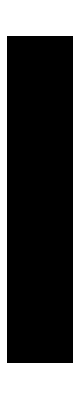
{-Graphics-,-Graphics--Graphics--Graphics--Graphics-}
{-Graphics-,-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-}
{-Graphics-,-Graphics--Graphics--Graphics--Graphics-}
{-Graphics-,-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-}
{-Graphics-,-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-}
{-Graphics-,-Graphics--Graphics--Graphics--Graphics--Graphics-}
{-Graphics-,-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-}
{-Graphics-,-Graphics--Graphics--Graphics--Graphics-}
{-Graphics-,-Graphics--Graphics--Graphics--Graphics-}
{-Graphics-,-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-}

```mathematica
Column[ParallelTable[With[{rule=res[[1]]},{k=AnalyzeRule[rule]["Colors"]},Pane[{
Labeled[ArrayPlot[CellularAutomaton[rule, {RandomInteger[{0, k-1}, 100], 0}, 100]], ClickToCopy[rule]], Row[Table[
Labeled[ArrayPlot[CellularAutomaton[rule, {IntegerDigits[init, k], 0}, 100]], ClickToCopy[init]]
, {init, res[[2, ;;UpTo[50]]]}], Spacer[1]]
}, 100000]], {res, RandomChoice[resultstodisplay, 10]}]]
```